```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PV/larin/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<renormAmpSquaredLarin.res
```

```mathematica
X[a_]:=norm
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;AL=1/137;
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
t1 =m^2-s/2-Sqrt[s] Sqrt[s-4 m^2]/2
```

-130.194

```mathematica
t2 =m^2-s/2+Sqrt[s] Sqrt[s-4 m^2]/2
```

-12.8864

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
t=-50
```

-50

```mathematica
ex[1]=Collect[Expand[renormAmpSquared//N],{A[___],B[___],C[___]}]
```

0.000247695 eps^3 Aconj(1.5) AS^3-0.000605684 eps^2 Aconj(1.5) AS^3-0.000283274 eps Aconj(1.5) AS^3-(0.0000217472 Aconj(1.5) AS^3)/eps+0.000736423 Aconj(1.5) AS^3+0.0000659303 eps^3 Aconj(4.9) AS^3-0.000365496 eps^2 Aconj(4.9) AS^3-0.0000856371 eps Aconj(4.9) AS^3+(6.65732×10^-6 Aconj(4.9) AS^3)/eps+0.00044439 Aconj(4.9) AS^3+0.00690352 eps^3 Bconj(12.3596,0.,0.) AS^3-0.00648342 eps^2 Bconj(12.3596,0.,0.) AS^3-0.00839367 eps Bconj(12.3596,0.,0.) AS^3+0.0078829 Bconj(12.3596,0.,0.) AS^3-0.000015778 eps^3 Bconj(12.3596,1.5,1.5) AS^3+0.000462216 eps^2 Bconj(12.3596,1.5,1.5) AS^3-0.000140116 eps Bconj(12.3596,1.5,1.5) AS^3+(0.000193685 Bconj(12.3596,1.5,1.5) AS^3)/eps-0.000561987 Bconj(12.3596,1.5,1.5) AS^3+0.000420596 eps^3 Bconj(12.3596,4.9,4.9) AS^3+0.000900215 eps^2 Bconj(12.3596,4.9,4.9) AS^3-0.000511384 eps Bconj(12.3596,4.9,4.9) AS^3-0.00109453 Bconj(12.3596,4.9,4.9) AS^3-0.000157662 eps^3 Bconj(51.9348,1.5,4.9) AS^3-0.000534515 eps^2 Bconj(51.9348,1.5,4.9) AS^3+0.000396604 eps Bconj(51.9348,1.5,4.9) AS^3-(0.000249141 Bconj(51.9348,1.5,4.9) AS^3)/eps+0.000649892 Bconj(51.9348,1.5,4.9) AS^3+0.000775377 eps^3 Bconj(51.9348,4.9,1.5) AS^3-0.000305215 eps^2 Bconj(51.9348,4.9,1.5) AS^3-0.000737835 eps Bconj(51.9348,4.9,1.5) AS^3-(0.000249141 Bconj(51.9348,4.9,1.5) AS^3)/eps+0.000371096 Bconj(51.9348,4.9,1.5) AS^3-0.00296832 eps^3 Bconj(76.7444,0.,4.9) AS^3-0.00304553 eps^2 Bconj(76.7444,0.,4.9) AS^3+0.00360905 eps Bconj(76.7444,0.,4.9) AS^3+0.00370292 Bconj(76.7444,0.,4.9) AS^3-0.00833646 eps^3 Bconj(76.7444,4.9,0.) AS^3+0.0126599 eps^2 Bconj(76.7444,4.9,0.) AS^3+0.0101359 eps Bconj(76.7444,4.9,0.) AS^3-0.0153926 Bconj(76.7444,4.9,0.) AS^3+0.00385049 eps^3 Bconj(131.891,0.,0.) AS^3-0.000679012 eps^2 Bconj(131.891,0.,0.) AS^3-0.00468163 eps Bconj(131.891,0.,0.) AS^3+0.00082558 Bconj(131.891,0.,0.) AS^3+0.000131598 eps^3 Bconj(131.891,1.5,1.5) AS^3-0.000252205 eps^2 Bconj(131.891,1.5,1.5) AS^3-0.000160004 eps Bconj(131.891,1.5,1.5) AS^3+0.000306644 Bconj(131.891,1.5,1.5) AS^3-0.0000280312 eps^3 Bconj(131.891,4.9,4.9) AS^3-0.0000733962 eps^2 Bconj(131.891,4.9,4.9) AS^3-0.000125218 eps Bconj(131.891,4.9,4.9) AS^3+(0.000193685 Bconj(131.891,4.9,4.9) AS^3)/eps+0.000089239 Bconj(131.891,4.9,4.9) AS^3-0.00833157 eps^3 Bconj(174.516,0.,1.5) AS^3+0.00346708 eps^2 Bconj(174.516,0.,1.5) AS^3+0.01013 eps Bconj(174.516,0.,1.5) AS^3-0.00421547 Bconj(174.516,0.,1.5) AS^3-0.00136623 eps^3 Bconj(174.516,1.5,0.) AS^3+0.000206737 eps^2 Bconj(174.516,1.5,0.) AS^3+0.00166114 eps Bconj(174.516,1.5,0.) AS^3-0.000251362 Bconj(174.516,1.5,0.) AS^3+0.00566287 eps^3 Bconj(225.,1.5,1.5) AS^3-0.0027876 eps^2 Bconj(225.,1.5,1.5) AS^3-0.00688522 eps Bconj(225.,1.5,1.5) AS^3+0.00338932 Bconj(225.,1.5,1.5) AS^3-0.00245662 eps^3 Bconj(225.,4.9,4.9) AS^3+0.00284943 eps^2 Bconj(225.,4.9,4.9) AS^3+0.0029869 eps Bconj(225.,4.9,4.9) AS^3-0.00346449 Bconj(225.,4.9,4.9) AS^3-0.00841027 eps^3 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+0.00190648 eps^2 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+0.0102257 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-0.002318 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+0.0470304 eps^3 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-0.038581 eps^2 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-0.0571821 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+0.0469089 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+0.00229272 eps^3 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+0.001519 eps^2 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-0.00278761 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-0.00184688 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-0.0287236 eps^3 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+0.00416092 eps^2 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+0.0349237 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-0.00505908 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+0.00334045 eps^3 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+0.00565584 eps^2 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-0.0040615 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-0.00687668 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+0.105512 eps^3 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-0.0423404 eps^2 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-0.128287 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+0.0514798 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-0.083262 eps^3 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+0.104572 eps^2 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+0.101234 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-0.127144 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-0.0104444 eps^3 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-0.0111554 eps^2 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+0.0126989 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+0.0135634 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+0.0563954 eps^3 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+0.0919826 eps^2 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-0.0685685 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-0.111837 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-0.0897271 eps^3 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+0.090404 eps^2 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+0.109095 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-0.109918 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+0.129301 eps^3 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-0.101283 eps^2 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-0.157211 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+0.123146 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-0.00673546 eps^3 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-0.000725846 eps^2 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+0.00818933 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+0.000882523 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+0.000381438 eps^3 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+0.000573445 eps^2 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-0.000463773 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-0.000697226 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-0.0057932 eps^3 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+0.000435962 eps^2 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+0.00704368 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-0.000530066 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-0.0991515 eps^3 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+0.0399656 eps^2 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+0.120554 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-0.0485923 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+0.00425373 eps^3 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-0.00390792 eps^2 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-0.00517191 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+0.00475146 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-0.15092 eps^3 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-0.013897 eps^2 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+0.183497 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+0.0168967 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-0.00750938 eps^3 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+0.00040942 eps^2 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+0.00913031 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-0.000497795 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-0.0028743 eps^3 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-0.000871924 eps^2 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+0.00349473 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+0.00106013 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-0.0602692 eps^3 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+0.0263505 eps^2 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+0.0732786 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-0.0320383 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-0.000448856 eps^3 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+0.00170684 eps^2 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+0.000545744 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-0.00207527 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+0.0178339 log(0.234375) AS^3+0.020037 log(0.765625) AS^3-0.0189354 log(0.0244141 mmu) AS^3-(0.00890595 AS^3)/eps-0.000403472 AS^3+0.00312116 AS^2+(0.000247695 eps^3 AS^3-0.000605684 eps^2 AS^3-0.000283274 eps AS^3-(0.0000217472 AS^3)/eps+0.000736423 AS^3) A(1.5)+(0.0000659303 eps^3 AS^3-0.000365496 eps^2 AS^3-0.0000856371 eps AS^3+(6.65732×10^-6 AS^3)/eps+0.00044439 AS^3) A(4.9)+(0.00690352 eps^3 AS^3-0.00648342 eps^2 AS^3-0.00839367 eps AS^3+0.0078829 AS^3) B(12.3596,0.,0.)+(-0.000015778 eps^3 AS^3+0.000462216 eps^2 AS^3-0.000140116 eps AS^3+(0.000193685 AS^3)/eps-0.000561987 AS^3) B(12.3596,1.5,1.5)+(0.000420596 eps^3 AS^3+0.000900215 eps^2 AS^3-0.000511384 eps AS^3-0.00109453 AS^3) B(12.3596,4.9,4.9)+(-0.000157662 eps^3 AS^3-0.000534515 eps^2 AS^3+0.000396604 eps AS^3-(0.000249141 AS^3)/eps+0.000649892 AS^3) B(51.9348,1.5,4.9)+(0.000775377 eps^3 AS^3-0.000305215 eps^2 AS^3-0.000737835 eps AS^3-(0.000249141 AS^3)/eps+0.000371096 AS^3) B(51.9348,4.9,1.5)+(-0.00296832 eps^3 AS^3-0.00304553 eps^2 AS^3+0.00360905 eps AS^3+0.00370292 AS^3) B(76.7444,0.,4.9)+(-0.00833646 eps^3 AS^3+0.0126599 eps^2 AS^3+0.0101359 eps AS^3-0.0153926 AS^3) B(76.7444,4.9,0.)+(0.00385049 eps^3 AS^3-0.000679012 eps^2 AS^3-0.00468163 eps AS^3+0.00082558 AS^3) B(131.891,0.,0.)+(0.000131598 eps^3 AS^3-0.000252205 eps^2 AS^3-0.000160004 eps AS^3+0.000306644 AS^3) B(131.891,1.5,1.5)+(-0.0000280312 eps^3 AS^3-0.0000733962 eps^2 AS^3-0.000125218 eps AS^3+(0.000193685 AS^3)/eps+0.000089239 AS^3) B(131.891,4.9,4.9)+(-0.00833157 eps^3 AS^3+0.00346708 eps^2 AS^3+0.01013 eps AS^3-0.00421547 AS^3) B(174.516,0.,1.5)+(-0.00136623 eps^3 AS^3+0.000206737 eps^2 AS^3+0.00166114 eps AS^3-0.000251362 AS^3) B(174.516,1.5,0.)+(0.00566287 eps^3 AS^3-0.0027876 eps^2 AS^3-0.00688522 eps AS^3+0.00338932 AS^3) B(225.,1.5,1.5)+(-0.00245662 eps^3 AS^3+0.00284943 eps^2 AS^3+0.0029869 eps AS^3-0.00346449 AS^3) B(225.,4.9,4.9)+(-0.00841027 eps^3 AS^3+0.00190648 eps^2 AS^3+0.0102257 eps AS^3-0.002318 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(0.0470304 eps^3 AS^3-0.038581 eps^2 AS^3-0.0571821 eps AS^3+0.0469089 AS^3) C[2.25,76.7444,40.96,4.9,1.5,0]+(0.00229272 eps^3 AS^3+0.001519 eps^2 AS^3-0.00278761 eps AS^3-0.00184688 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(-0.0287236 eps^3 AS^3+0.00416092 eps^2 AS^3+0.0349237 eps AS^3-0.00505908 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(0.00334045 eps^3 AS^3+0.00565584 eps^2 AS^3-0.0040615 eps AS^3-0.00687668 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(0.105512 eps^3 AS^3-0.0423404 eps^2 AS^3-0.128287 eps AS^3+0.0514798 AS^3) C[2.25,174.516,225,1.5,1.5,0]+(-0.083262 eps^3 AS^3+0.104572 eps^2 AS^3+0.101234 eps AS^3-0.127144 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(-0.0104444 eps^3 AS^3-0.0111554 eps^2 AS^3+0.0126989 eps AS^3+0.0135634 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(0.0563954 eps^3 AS^3+0.0919826 eps^2 AS^3-0.0685685 eps AS^3-0.111837 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(-0.0897271 eps^3 AS^3+0.090404 eps^2 AS^3+0.109095 eps AS^3-0.109918 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(0.129301 eps^3 AS^3-0.101283 eps^2 AS^3-0.157211 eps AS^3+0.123146 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(-0.00673546 eps^3 AS^3-0.000725846 eps^2 AS^3+0.00818933 eps AS^3+0.000882523 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(0.000381438 eps^3 AS^3+0.000573445 eps^2 AS^3-0.000463773 eps AS^3-0.000697226 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(-0.0057932 eps^3 AS^3+0.000435962 eps^2 AS^3+0.00704368 eps AS^3-0.000530066 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(-0.0991515 eps^3 AS^3+0.0399656 eps^2 AS^3+0.120554 eps AS^3-0.0485923 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(0.00425373 eps^3 AS^3-0.00390792 eps^2 AS^3-0.00517191 eps AS^3+0.00475146 AS^3) C[76.7444,24.01,12.3596,4.9,4.9,0]+(-0.15092 eps^3 AS^3-0.013897 eps^2 AS^3+0.183497 eps AS^3+0.0168967 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(-0.00750938 eps^3 AS^3+0.00040942 eps^2 AS^3+0.00913031 eps AS^3-0.000497795 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(-0.0028743 eps^3 AS^3-0.000871924 eps^2 AS^3+0.00349473 eps AS^3+0.00106013 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(-0.0602692 eps^3 AS^3+0.0263505 eps^2 AS^3+0.0732786 eps AS^3-0.0320383 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(-0.000448856 eps^3 AS^3+0.00170684 eps^2 AS^3+0.000545744 eps AS^3-0.00207527 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(0.0160124+0.053108 ⅈ) eps^2 AS^3+(0.0022955-1.03219×10^-19 ⅈ) eps^2 log^2(mmu) AS^3+(0.00456388+3.25261×10^-19 ⅈ) eps log^2(mmu) AS^3+(4.4066×10^-17+1.18563×10^-20 ⅈ) log^2(mmu) AS^3-(0.0112868+1.38778×10^-17 ⅈ) eps AS^3+(0.0102257-4.33681×10^-19 ⅈ) eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-0.002318 C[2.25,12.3596,2.25,0,1.5,0] AS^3-(0.0571821-6.16298×10^-33 ⅈ) eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(0.0469089-3.08149×10^-33 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(0.00278761-9.62965×10^-35 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-0.00184688 C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(0.0349237+1.73472×10^-18 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3-(0.00505908-4.33681×10^-19 ⅈ) C[2.25,131.891,174.516,0,1.5,0] AS^3-(0.0040615-2.1684×10^-19 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(0.00687668-4.33681×10^-19 ⅈ) C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(0.128287-1.38778×10^-17 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+(0.0514798-3.46945×10^-18 ⅈ) C[2.25,174.516,225,1.5,1.5,0] AS^3+(0.101234-9.24446×10^-33 ⅈ) eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(0.127144+6.93889×10^-18 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3+0.0126989 eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(0.0135634-8.67362×10^-19 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-(0.0685685-6.93889×10^-18 ⅈ) eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-(0.111837-2.08167×10^-17 ⅈ) C[24.01,76.7444,225,4.9,4.9,0] AS^3+0.109095 eps C[24.01,131.891,24.01,0,4.9,0] AS^3-(0.109918-6.93889×10^-18 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3-(0.157211+6.93889×10^-18 ⅈ) eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(0.123146-2.08167×10^-17 ⅈ) C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(0.00818933-4.33681×10^-19 ⅈ) eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+(0.000882523+5.42101×10^-20 ⅈ) C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-(0.000463773-2.71051×10^-20 ⅈ) eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(0.000697226+2.71051×10^-20 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+(0.00704368-5.77779×10^-34 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(0.000530066-2.71051×10^-20 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+(0.120554-6.93889×10^-18 ⅈ) eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(0.0485923-3.46945×10^-18 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(0.00517191-6.50521×10^-19 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(0.00475146-2.1684×10^-19 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(0.183497-2.08167×10^-17 ⅈ) eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+(0.0168967-1.73472×10^-18 ⅈ) C[76.7444,24.01,225,4.9,4.9,0] AS^3+0.00913031 eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(0.000497795-5.42101×10^-20 ⅈ) C[174.516,2.25,131.891,1.5,1.5,0] AS^3+(0.00349473-1.92593×10^-34 ⅈ) eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(0.00106013-1.0842×10^-19 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(0.0732786-6.93889×10^-18 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(0.0320383+1.73472×10^-18 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3+0.000545744 eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-(0.00207527+1.0842×10^-19 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(0.0102257-4.33681×10^-19 ⅈ) eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-0.002318 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(0.0571821-6.16298×10^-33 ⅈ) eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(0.0469089-3.08149×10^-33 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(0.00278761-9.62965×10^-35 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-0.00184688 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(0.0349237+1.73472×10^-18 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(0.00505908-4.33681×10^-19 ⅈ) Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(0.0040615-2.1684×10^-19 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(0.00687668-4.33681×10^-19 ⅈ) Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(0.128287-1.38778×10^-17 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(0.0514798-3.46945×10^-18 ⅈ) Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(0.101234-9.24446×10^-33 ⅈ) eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(0.127144+6.93889×10^-18 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+0.0126989 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(0.0135634-8.67362×10^-19 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-(0.0685685-6.93889×10^-18 ⅈ) eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(0.111837-2.08167×10^-17 ⅈ) Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+0.109095 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(0.109918-6.93889×10^-18 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(0.157211+6.93889×10^-18 ⅈ) eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(0.123146-2.08167×10^-17 ⅈ) Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(0.00818933-4.33681×10^-19 ⅈ) eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+(0.000882523+5.42101×10^-20 ⅈ) Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-(0.000463773-2.71051×10^-20 ⅈ) eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(0.000697226+2.71051×10^-20 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+(0.00704368-5.77779×10^-34 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(0.000530066-2.71051×10^-20 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+(0.120554-6.93889×10^-18 ⅈ) eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(0.0485923-3.46945×10^-18 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(0.00517191-6.50521×10^-19 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(0.00475146-2.1684×10^-19 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(0.183497-2.08167×10^-17 ⅈ) eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(0.0168967-1.73472×10^-18 ⅈ) Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+0.00913031 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(0.000497795-5.42101×10^-20 ⅈ) Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+(0.00349473-1.92593×10^-34 ⅈ) eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(0.00106013-1.0842×10^-19 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(0.0732786-6.93889×10^-18 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(0.0320383+1.73472×10^-18 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+0.000545744 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-(0.00207527+1.0842×10^-19 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-(0.020702+0.00971582 ⅈ) eps^2 log(mmu) AS^3+(0.0165941-6.93889×10^-18 ⅈ) eps log(mmu) AS^3+((8.80508×10^-17-9.24446×10^-33 ⅈ) log(mmu) AS^3)/eps-(0.0100295-1.14701×10^-18 ⅈ) log(mmu) AS^3-(2.87954×10^-13 AS^3)/eps+((8.79881×10^-17+1.21832×10^-20 ⅈ) AS^3)/eps^2+(0.0557844+3.1984×10^-18 ⅈ) AS^3+(0.00312116-2.1684×10^-19 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC]]]
```

-0.0100295 AS^3 log(mmu)+0.0254507 AS^3+0.00312116 AS^2

```mathematica
LOsquared[s_,t_]:=+AL^2*(+32768/81*m^2*s^(-5)*t^2*r^(-6)*pi^4*AS^2+32768/81*m^2*s^(-4)*t*r^(-6)*pi^4*AS^2+16384/81*m^2*s^(-3)*r^(-6)*pi^4*AS^2-65536/81*m^4*s^(-5)*t*r^(-6)*pi^4*AS^2-65536/81*m^4*s^(-4)*r^(-6)*pi^4*AS^2+32768/81*m^6*s^(-5)*r^(-6)*pi^4*AS^2+131072/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^(-5)*t^2*pi^4*AS^2+131072/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^(-4)*t*pi^4*AS^2+65536/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^(-3)*pi^4*AS^2-262144/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^4*s^(-5)*t*pi^4*AS^2-262144/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^4*s^(-4)*pi^4*AS^2+131072/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^6*s^(-5)*pi^4*AS^2-131072/81/(1-3*r+3*r^2-r^3)*m^2*s^(-5)*t^2*r^(-3)*pi^4*AS^2-131072/81/(1-3*r+3*r^2-r^3)*m^2*s^(-4)*t*r^(-3)*pi^4*AS^2-65536/81/(1-3*r+3*r^2-r^3)*m^2*s^(-3)*r^(-3)*pi^4*AS^2+262144/81/(1-3*r+3*r^2-r^3)*m^4*s^(-5)*t*r^(-3)*pi^4*AS^2+262144/81/(1-3*r+3*r^2-r^3)*m^4*s^(-4)*r^(-3)*pi^4*AS^2-131072/81/(1-3*r+3*r^2-r^3)*m^6*s^(-5)*r^(-3)*pi^4*AS^2)
```

```mathematica
ex[4]=Collect[Chop[ex[3]],AS]/.{AS-> z *0.3}//Expand
```

-0.000270797 z^3 log(mmu)+0.000687169 z^3+0.000280904 z^2

```mathematica
ratioAmpSquare[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

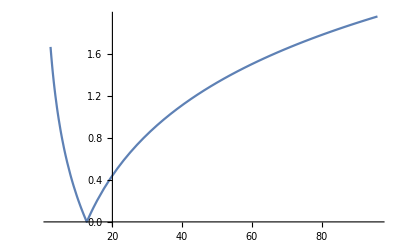

```mathematica
Plot[ratioAmpSquare[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioAmpSquare[(2mc)^2]
```

0.328113

```mathematica
ratioAmpSquare[(m)^2]
```

1.13273

```mathematica
LOsquared[s,t]/.{AS-> z *0.3}//Expand
```

0.000280904 z^2

```mathematica
LOsquared[s,tt]/AS^2/kinfactor[s,tt]/.{tt-> -50}
```

0.00312116/(kinfactor(225,-50))

```mathematica
Plot[LOsquared[s,tt]/AS^2/kinfactor[s,tt],{tt,t1,t2}]
```

-Graphics-

```mathematica
AmpSquareRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

1.13273

```mathematica
kinfactor[s_,t_]:=+2*s*t^2+2*s^2*t+s^3-4*m^2*s*t-4*m^2*s^2+2*m^4*s
```

```mathematica
Expand[ex[4]/kinfactor[s,t]]
```

-1.54133×10^-10 z^3 log(mmu)+3.91126×10^-10 z^3+1.59886×10^-10 z^2

```mathematica
FullSimplify[LOsquared[s,t]/kinfactor[s,t]]
```

1.77652×10^-9 AS^2

```mathematica
LO2=+AL^2*(-16384/81*m^2*s^-6*r^-6*pi^4*AS^2-65536/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^-6*pi^4*AS^2+65536/81/(1-3*r+3*r^2-r^3)*m^2*s^-6*r^-3*pi^4*AS^2)
```

-1.77652×10^-9 AS^2

```mathematica
FullSimplify[LO2]
```

-1.77652×10^-9 AS^2

```mathematica
FullSimplify[LOsquared[s,t]/kinfactor[s,t]/LO2]
```

-1.